## Bayesian Statistics, Assignment for Tuesday, Oct. 1

## Reading

Study to the end of Chapter 2 of our Bayesian statistics book.

## For Problem Set 8

### χ^2 for Bad Fits

In Friday’s class, we did linear regression to get the best fit. It came up that people would like to know what happens if the fit is lousy, and I heartily agree that that might help  build your intuition. So the first three problems of this problem set are about different kinds of bad fits.

#### Problem 1. Bad Fit Due to Wrong Intercept — b-Value too Low

Let’s go back to our three water pressure measurements:

59 psi at 15 minutes
61.5 psi at 25 minutes
63.5 psi at 35 minutes

Let’s add error bars! It is common to put error bars on the plot representing ±1σ of deviation above and below each data point. We’ll  say that σ=0.5 psi. So the first data point should show up with error bars that extend from 58.5 psi to 59.5 psi, etc.

Now, I am going to add a little to the b-value so that we no longer have the best fit.

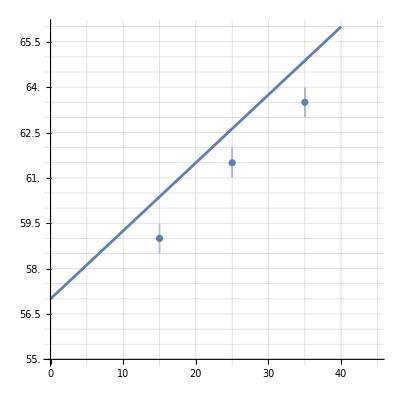

```mathematica
Show[Plot[0, {t, 0, 45}, PlotRange->{{0, 45},{55,66}}, Ticks->{Range[0,45, 5],Range[55, 66, 0.5]},GridLines->{Range[0,45, 5],Range[55, 66, 0.5]}, GridLinesStyle->Medium,AspectRatio->1], ListPlot[{{15, Around[59,0.5]}, {25, Around[61.5,0.5]}, {35, Around[63.5,0.5]}}, PlotRange->{{0,45},{55, 66}}],Plot[0.225*t + 57, {t, 0, 45}, PlotRange->{{0, 45},{55, 66}}]]
```

(a) Estimate the three deviations. To get you started, I’ll fill in my estimate of the first one.

d_1=-1.4 psi

d_2=

d_3=

(b) Square the deviations and divide them by σ^2=(0.5 psi)^2=0.25 psi^2:

d_1^2/σ^2=(1.96 psi^2)/(0.25 psi^2)=7.84

d_2^2/σ^2=

d_3^2/σ^2=

(c) Compute χ^2 which is just the sum of the three quantities you computed in (b). Note that the units canceled out. χ^2 is always dimensionless.

χ^2=

DISCUSSION: If this were a good fit, you would expect to get a χ^2 of about N=3. Since the χ^2 is substantially larger than that, this is a bad fit. [NB: It is a tad more complicated than that, and you can ask why in class, because I am not going to write a mini-essay about it right here.]

#### Problem 2. Bad Fit Due to Wrong Slope — a-Value too High

Now, I am going to add a little to the a-value to make another lousy fit. I also subtracted some from b or the fit would have been really lousy.

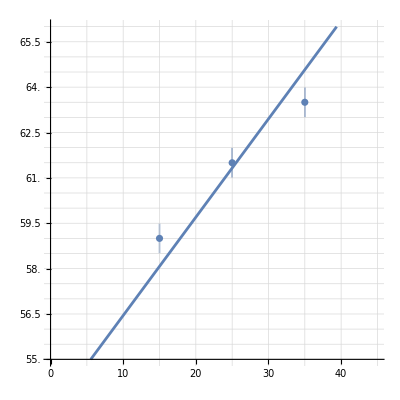

```mathematica
Show[Plot[0, {t, 0, 45}, PlotRange->{{0, 45},{55,66}}, Ticks->{Range[0,45, 5],Range[55, 66, 0.5]},GridLines->{Range[0,45, 5],Range[55, 66, 0.5]}, GridLinesStyle->Medium,AspectRatio->1], ListPlot[{{15, Around[59,0.5]}, {25, Around[61.5,0.5]}, {35, Around[63.5,0.5]}}, PlotRange->{{0,45},{55, 66}}],Plot[0.325*t + 53.2, {t, 0, 45}, PlotRange->{{0, 45},{55, 66}}]]
```

(a) Again, estimate the three deviations. To get you started, I’ll say that the first one looks like 1.0 psi.

d_1=1.0 psi

d_2=

d_3=

(b) Again, square the deviations and divide them by σ^2=0.25 psi^2:

d_1^2/σ^2=1.00/0.25=4.00

d_2=

d_3=

(c) Again, compute χ^2:

χ^2=

Since the χ^2 is substantially larger than 3, this is another bad fit.

#### Problem 3. Bad Fit Due to Wrong Function —Linear Fit to Quadratic Data

If you throw a ball up in the air, its height follows a quadratic formula (our theoretical model):

h(t)=h_0+v_0 t-1/2 g t^2

Let’s use these values for h_0, v_0, and g:

h_0=5m
v_0=20m/s
g=10m/s^2

I’ll plug in t_0=0s, t_1=1s, t_2=2s, and t_3=3s, into the formula and get:

h_0=5m
h_1=20m
h_2=25m
h_3=20m

These data points are perfect (because I got them by plugging in to the theoretical model), and so a parabola would fit perfectly to them, but let’s make a terrible fit by trying to fit the data to a linear function.

(a) Below, fill in the values that I didn’t fill in. Feel free to drag all the units around, or make your life easy and leave the units off! I can assure you that if you leave the units off at all the intermediate steps, that in the end, the units of a would work out to be m/s and the units of b would be m.

M_aa=∑_(i=1)^N t_i^2=
M_ab=∑_(i=1)^N t_i= 0 + 1 + 2 + 3 =6
M_bb=∑_(i=1)^N 1=N=4
M_a=∑_(i=1)^N h_i t_i=
M_b=∑_(i=1)^N h_i=5 + 20 + 25 + 20=70

(b) Use your results to compute a and b. After you have gotten answers for a and b, stick the right units on them.

a=(M_bb M_a-M_ab M_b)/(M_aa M_bb-M_ab^2)=

and

b=(M_aa M_b-M_ab M_a)/(M_aa M_bb-M_ab^2)=

(c) Let’s just say that σ=1m is our measurement error for each height. I have put the data on the graph below. On top of the data,  graph your best fit using the function h=a·t+b.

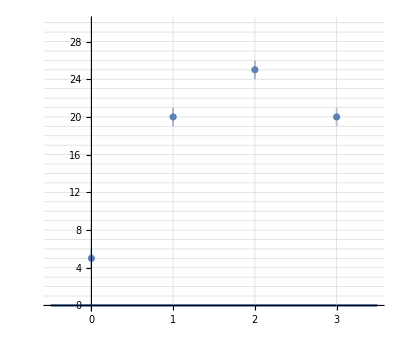

```mathematica
Show[Plot[0, {t, -0.5, 3.5}, PlotRange->{{-0.5, 3.5},{0,30}}, Ticks->{Range[0,3, 1],Range[0, 30, 1]},GridLines->{Range[0,3, 1],Range[0, 30, 1]}, GridLinesStyle->Medium,AspectRatio->0.85], ListPlot[{{0, Around[5,1]}, {1, Around[20,1]}, {2, Around[25,1]}, {3, Around[20,1]}}, PlotRange->{{-0.5, 3.5},{0, 30}}]]
```

(d) Write down the four deviations. To get you started, I’ll tell you that if you did everything right, the deviation at t_0=0s is the value I filled in below.

d_0=-5m

d_1=

d_2=

d_3=

(e) Square the deviations and divide them by σ^2=1 m^2:

d_0^2/σ^2=(5m)^2/(1m)^2=25

d_1^2/σ^2=

d_2^2/σ^2=

d_3^2/σ^2=

(f) Compute χ^2 which is just the sum of the four quantities you computed in (e).

χ^2=

If this were a good fit, you would expect to get a χ^2 of about 4 since there are four data points. This is a terrible fit!

### Conjoint Tables

#### Problem 4. The Harvester, the Rocks, and the Potatoes

By the time you get to p. 20 of the reading, you will see that conjoint tables are a pretty useful tool, at least for analyzing simple situations. Let’s practice with the numbers from the last problem set. 1000 nodules were harvested from the field. The field contains 9x as many rocks as potatoes. Of the potatoes, 95% get sorted correctly. Of the rocks, unfortunately, 20% of those get sorted incorrectly.

(a) Using this data, make a conjoint table whose margins add up to 1000. I gave you a nice empty table to fill in.

```mathematica
data=Table[If[i==3 && j==3, 1000, "              "],{i,3},{j,3}];
table1 = Prepend[data, {"Is a Rock", "Is a Potato", "Is a Nodule"}];
table2 = MapThread[Prepend,{table1, {"","Discarded", "Sent to Kitchen", "Sum"}}];
Grid[table2, Frame->All]
```

| Is a Rock | Is a Potato | Is a Nodule
Discarded |                |                |               
Sent to Kitchen |                |                |               
Sum |                |                | 1000

(b) Now use the same data to make a conjoint table that is normalized so that the margins add up to 1.000.

```mathematica
data=Table[If[i==3 && j==3, "1.000", "              "],{i,3},{j,3}];
table1 = Prepend[data, {"Is a Rock", "Is a Potato", "Is a Nodule"}];
table2 = MapThread[Prepend,{table1, {"","Discarded", "Sent to Kitchen", "Sum"}}];
Grid[table2, Frame->All]
```

| Is a Rock | Is a Potato | Is a Nodule
Discarded |                |                |               
Sent to Kitchen |                |                |               
Sum |                |                | 1.000

(c) Finally, use the same data one more time to make a conjoint table that is normalized so that the margins add up to 100.0%.

```mathematica
data=Table[If[i==3 && j==3, "100.0%", "              "],{i,3},{j,3}];
table1 = Prepend[data, {"Is a Rock", "Is a Potato", "Is a Nodule"}];
table2 = MapThread[Prepend,{table1, {"","Discarded", "Sent to Kitchen", "Sum"}}];
Grid[table2, Frame->All]
```

| Is a Rock | Is a Potato | Is a Nodule
Discarded |                |                |               
Sent to Kitchen |                |                |               
Sum |                |                | 100.0%

DISCUSSION: It is worthwhile to simply notice where the percentages in the original story ended up in the final table.